```mathematica
Solve[S1*d==-(-σ-S1)*(d-t),S1]
```

{{S1→((d-t) σ)/t}}

```mathematica
S2=-σ-((d-t) σ)/t//FullSimplify
```

-(d σ)/t

```mathematica
-((d-t) σ)/t/.{d->t/2}
```

σ/2

```mathematica
(2*d-t)/t/.{d->t/2}
```

0

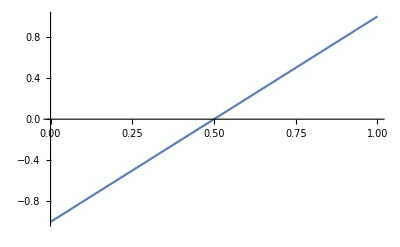

```mathematica
Plot[2*d-1,{d,0,1}]
```

```mathematica
ϕ[x_,y_,z_]:=1/Sqrt[x^2+(y-1)^2+z^2]-1/Sqrt[1/Sqrt[x^2+(y+1)^2+z^2]]
```

```mathematica
(*Different problem now*)
```

```mathematica
ϕ[ρ_,z_,j_]:=1/Sqrt[ρ^2+(z-(-2*L*j+d))^2]-1/Sqrt[ρ^2+(z+(2*L*(j+1)+d))^2];
```

```mathematica
D[ϕ[ρ,z,j],z]/.{z->0}
```

-(-d+2 j L)/(((-d+2 j L)^2+ρ^2)^(3/2))+(d+2 (1+j) L)/(((d+2 (1+j) L)^2+ρ^2)^(3/2))

```mathematica
Integrate[(-(-d+2 j L)/(((-d+2 j L)^2+ρ^2)^(3/2))+(d+2 (1+j) L)/(((d+2 (1+j) L)^2+ρ^2)^(3/2)))*ρ,{ρ,0,Infinity}]
```

ConditionalExpression[(d-2 j L)/(√((d-2 j L)^2))+(d+2 (1+j) L)/(√((d+2 (1+j) L)^2)), Re[(d-2 j L)^2]>0&&Re[(d+2 (1+j) L)^2]>0]

```mathematica
Sum[(d-2 j L)/(√((d-2 j L)^2))+(d+2 (1+j) L)/(√((d+2 (1+j) L)^2)),{j,-Infinity,Infinity}]
```

∑_(j=-∞)^∞ ((d-2 j L)/(√((d-2 j L)^2))+(d+2 (1+j) L)/(√((d+2 (1+j) L)^2)))

```mathematica
Sum[1/Sqrt[ρ^2+(z-(-2*L*j+d))^2],{j,-Infinity,Infinity}]
```

Sum::div: Sum does not converge.

∑_(j=-∞)^∞ 1/(√((-d+2 j L+z)^2+ρ^2))

```mathematica
Integrate[1/Sqrt[t^2-1]*Exp[-t*x],{t,1,Infinity}]
```

ConditionalExpression[BesselK[0,x], Re[x]>0]

```mathematica
ϕ=Q*Cos[Pi*z/L]*Cos[Pi*d/L]*Exp[-Pi*ρ/L]*Sqrt[8/(ρ*L)];
```

```mathematica
Integrate[ρ*D[ϕ,z]/.{z->d},{ρ,0,Infinity}]
```

ConditionalExpression[-(√(1/L) √L Q Sin[(2 d π)/L])/(√2), Re[L]>0]

```mathematica
ϕ[ρ_,z_,n_]:=(-1)^n/Sqrt[ρ^2+(z-(-1)^n*d+n*L)^2]
```

```mathematica
D[ϕ[ρ,z,n],z]/.{z->-L/2}
```

((-1)^(1+n) ((-1)^(1+n) d-L/2+L n))/((((-1)^(1+n) d-L/2+L n)^2+ρ^2)^(3/2))

```mathematica
Integrate[((-1)^(1+n) ((-1)^(1+n) d-L/2+L n))/((((-1)^(1+n) d-L/2+L n)^2+ρ^2)^(3/2))*ρ,{ρ,0,Infinity}]
```

ConditionalExpression[((-1)^n (2 (-1)^n d+L-2 L n))/(√((2 (-1)^n d+L-2 L n)^2)), Re[(2 (-1)^n d+L-2 L n)^2]>0]

```mathematica
Solve[{A1+A2==q,A1-A2==-q*Sqrt[R1*R2]/R0},{A1,A2}]
```

{{A1→-(q (-R0+√(R1 R2)))/(2 R0),A2→(q (R0+√(R1 R2)))/(2 R0)}}

```mathematica
-(q (-R0+√(R1 R2)))/(2 R0)*(R1/R2)^(n/2)//FullSimplify
```

(q (R1/R2)^(n/2) (R0-√(R1 R2)))/(2 R0)

```mathematica
Sum[(-(q (-R0+√(R1 R2)))/(2 R0)+(-1)^n*(q (R0+√(R1 R2)))/(2 R0))*(R1/R2)^(n/2),{n,1,Infinity}]//FullSimplify
```

(q (-R0 R1+√(R1/R2) R2 √(R1 R2)))/(R0 (R1-R2))

```mathematica
Solve[{B1+B2==R0,B1-B2==R2*R1/R0},{B1,B2}]
```

{{B1→-(-R0^2-R1 R2)/(2 R0),B2→-(-R0^2+R1 R2)/(2 R0)}}

```mathematica
R2(R0-R1)+R1(R2-R0)//FullSimplify
```

R0 (-R1+R2)